Remove::rmnsm: There are no symbols matching ""Global`*"".

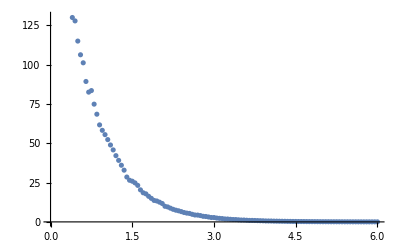

{a→251.707,b→1.52874}

{c→3.27067×10^-11}

```mathematica
Remove["Global`*"]
data=Import["/Users/Felix/GitHub/Envariabel-projekt/matserie.dat"];
ListPlot[data]
FindFit[data, a ⅇ^(- b x), {a,b}, x]
FindFit[data,251.70653701301623 ⅇ^(-t/(20000000000 c)) , c,t]
data[[All,2]];
```

```mathematica
Remove["Global`*"]
R=20*10^9;
DSolve[{u'[t]+u[t]*1/(R*c)==0}, u[t], t]
```

{{u[t]→ⅇ^(-t/(20000000000 c)) C[1]}}

```mathematica
Remove["Global`*"]
R=20*10^9;
C0=3.27*10^-11;


D[251.707*ⅇ^(-t/(R*C0))]*C0
```

8.23082×10^-9 ⅇ^(-1.52905 t)

```mathematica
Remove["Global`*"]
c=3.270666888845813*^-11;
Solve[u==251.70653701301623 ⅇ^(-t/(20000000000 (c/2))) ,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→-0.327067 Log[0.00397288 u]}}

```mathematica
Remove["Global`*"]
```

```mathematica
i[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
i[0]
Solve[4.11540945*^-9==8.2308189*^-9 ⅇ^(-1.529051987767584t),t]
```

8.23082×10^-9

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.453318}}

```mathematica
(8.2308189*^-9)/2
```

4.11541×10^-9

```mathematica
Remove["Global`*"]
q[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
q[0];
Solve[q[0]/2==q[t],t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.453318}}

```mathematica
Remove["Global`*"]
c=3.270666888845813*^-11;
i[t_]=8.2308189*^-9 ⅇ^(-1.529051987767584t);
u[t_]=251.70653701301623 ⅇ^(-t/(20000000000 c)) ;
p[t_]=u[t]*i[t];
En[t_]=p[t]*t;
Limit[p[t],t->Infinity]
Limit[Integrate[En[t],{t,0,R}], R->Infinity]
```

0.

2.21575×10^-7

```mathematica
Remove["Global`*"]
c0=3.270666888845813*^-11;
c=c0*1.1
DSolve[{R* q'[t]+q[t]/c==250,q[0]==c0*250},q[t],t]
FullSimplify[%]
```

3.59773×10^-11

{{q[t]→8.99433×10^-9 ⅇ^(-(2.77953×10^10 t)/R) (-0.0909091+1. ⅇ^((2.77953×10^10 t)/R))}}

{{q[t]→8.99433×10^-9-8.17667×10^-10 ⅇ^(-(2.77953×10^10 t)/R)}}

```mathematica
Remove["Global`*"]
q[t_]=8.994333944325988*^-9 ⅇ^(-(2.7795276620534058*^10 t)/R) (-0.09090909090909122+1. ⅇ^((2.7795276620534058*^10 t)/R));
i[t_]=D[q[t],t];
FullSimplify[%];
i[250*10^-6];
FullSimplify[%]
```

```mathematica
Solve[(22.72727272727281 ⅇ^(-6.948819155133515*^6/R))/R==1*10^-6,R]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{R→3.99964×10^6},{R→1.3671×10^7}}